```mathematica
Clear["Global'*"]
Ro[A_,W_]=√((Lm*Lh*bh*(ⅇ^-(A))*bm*(ⅇ^-(A))*alph*alpm*(1-(12.58/(K*(ⅇ^-(W+A))))))/(mum*(ⅇ^(W))*muh*((mum*(ⅇ^(W)))+phim)*(muh+phih+gh)*(alph+muh)*(alpm+(mum*(ⅇ^(W))))))
```

0.349142 √((ⅇ^(-2 A-W) (1-0.1258 ⅇ^(A+W)))/((0.00530857+0.025 ⅇ^W) (0.1428+0.025 ⅇ^W)))

```mathematica
(*Define Fixed Parameters*)(*Human Population Parameters*)Lh=0.000046;   (*Growth rate*)
b1=0.75;
bh=b1;  (*Infection rate by mosquito bites*)
alph=0.1667;   (*Rate from exposed to infected*)
gh=0.328833;   (*Recovery rate*)
muh=0.000046;  (*Natural death rate*)
phih=0.0005;
T=0.0005;

(*Mosquito Population Parameters*)
Lm=0.025;    (*Growth rate*)
b2=0.375;
bm=b2;  (*Infection rate by biting infected humans*)
alpm=0.1428;   (*Rate from exposed to infected*)
μ2=0.025;
mum=μ2;
phim=0.00530856625;
K=100;
```

√((alph alpm bh bm ⅇ^(-2 A-W) (1-(12.58 ⅇ^(A+W))/K) Lh Lm)/(muh (alph+muh) mum (alpm+ⅇ^W mum) (gh+muh+phih) (ⅇ^W mum+phim)))

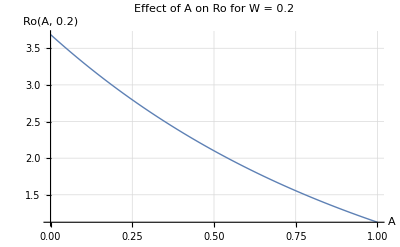

```mathematica
Plot[Ro[A,0.2],{A,0,1},AxesLabel->{"A","Ro(A, 0.2)"},PlotLabel->"Effect of A on Ro for W = 0.2",PlotStyle->Thick,GridLines->Automatic]
```

```mathematica
Manipulate[Plot[Ro[A,W],{A,0,1},AxesLabel->{"A","Ro(A, W)"},PlotLabel->"Effect of A on Ro for Different W",PlotStyle->Thick,GridLines->Automatic],{W,0,1}  (*Interactive slider for W from 0 to 1*)]
```

```mathematica
Plot3D[Ro[A,W],{A,0,1},{W,0,1},AxesLabel->{"A","W","Ro"},PlotLabel->"Effect of A and W on Ro",ColorFunction->"Rainbow",Mesh->None,PlotStyle->Opacity[0.8]]
```

-Graphics3D-